```mathematica
For[n = 3, n <= 7, n ++,
For[k = 0, k <= n,k++,
Print[N[Binomial[n,k]Subfactorial[n-k]/Factorial[n] - 1/Factorial[k]/E, 2]]]]
```

6

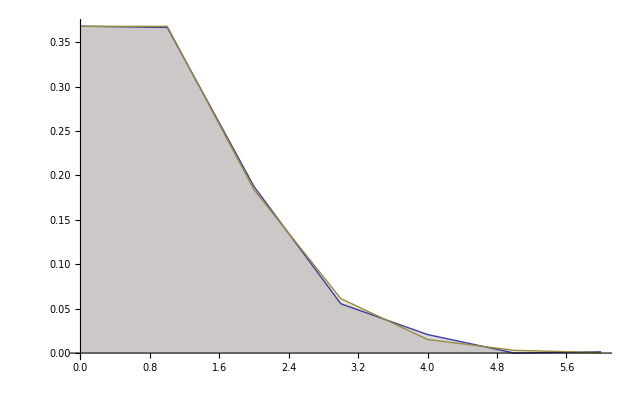

```mathematica
n=6
DiscretePlot[{Binomial[n,k]*Subfactorial[n-k]/Factorial[n] ,,1/E/Factorial[k]},{k,0,n},Joined->True,BaseStyle->{FontWeight->"Bold",FontSize->21},AxesOrigin->{0,0}]
```